## Init

```mathematica
NilsSolToMySol[nilssol_List, mval_Integer, nval_Integer, spin_?NumericQ, pol_Integer]:=
Block[{anglcoeffs, anglfunc, anglfunctmp,μNv, ν,ω,rsol, frobeniusexp},
anglcoeffs = nilssol[[1]][[All,2]];
anglfunctmp = (nilssol[[2]]/.QNMcode`θ->θ);
anglfunc = {θ}|->anglfunctmp//Evaluate;
μNv = nilssol[[3]];
ν = (QNMcode`rν+I*QNMcode`iν)/.nilssol[[4]];
ω = nilssol[[5]];
rsol =( QNMcode`R/.nilssol[[6]]);
frobeniusexp = nilssol[[7]];
<|"Parameters"-><|"m"->mval, "n"->nval, "χ"->spin, "s"->pol, "μNv"->μNv|>, "Solution"-><|"R"->rsol, "S"->anglfunc, "Scoeffs"->anglcoeffs, "ν"->ν, "ω"->ω|>|>
]
$root = NotebookDirectory[];
SetDirectory[$root];
$FKKSRoot = $root<>"../../../";
Import[$FKKSRoot<>"Packages/HelperFunctions.wl"];
$SolutionPath = $FKKSRoot<>"Solutions/";
```

## QNM Evaluator

```mathematica
Import[$root<>"nonR_master.wl"]
```

## Teukolsky Evaluator

```mathematica
Block[{Print},
<<HelperFunctions.wl;
<<BHEvol.m;
<<VectorFieldNorm.m;
<<SpinWeightedSpheroidalHarmonics.m;
<<RenormalizedAngularMomentum.m;
<<MSTformalism.m;
<<WeylPsi4.m;
<<TeukolskyT.m;
<<TeuInter.wl;
]
```

rstop::shdw: Symbol rstop appears in multiple contexts {VectorFieldNorm`,Global`}; definitions in context VectorFieldNorm` may shadow or be shadowed by other definitions.

```mathematica
res = <||>;
TeuCode[1,0,9/10,0.3,1, MySolution->True];
res["MyEinf"]= TeuInterEnv`out10["Derived"]["NormalizedEinf"]
```

________My solution________

Data import: 
	 input mass: 0.29999999999999998889776975374843459576`25.
	 mass: 3/10
	 BH Spin: 0.9`25.
	 Mode: 1
	 Overtone: 0
	 Frequency: 0.28363236035996286959257196597021742589`18. + 0.00004647996908679003038969342945379168`18.*I
	 Eigenvalue: -12110275895101/30612519292533 - (41369622953*I)/973680004991357

Radsol[2]: 1.75195393646596157890189391737329006849`24.194157688060024 - 0.29566605073514228233981362446321252154`24.386693892603752*I

Angsol[2]: -0.314167824063651 + 3.009058270484037*^-8*I

precision: 25

rplus = 1.435889894354067355223698

rstart = 1.445889894354067355223698

epsilonr = 0.006964322291925094379954

rstop = 663.6666666666667160099122

r glue = 79.64

Interpolation: Start.

rmesh = 199

Thetamesh = 99

ThetaStart = 0.00001503281771187976300491185

ThetaStop = 3.141580946007195951352742

Exponential extension: Start.

Solution at horizon: Test:

Rad[rtst] = 0.91754959011808564237842 - 0.4340685118535344071916 I

Exponential extension: Done!

Generating Interpolating functions for A_μ

xAct`xTensor`PrintAsCharacter::argx: xAct`xTensor`PrintAsCharacter called with 0 arguments; 1 argument is expected.

Data produced for: 1

xAct`xTensor`PrintAsCharacter::argx: xAct`xTensor`PrintAsCharacter called with 0 arguments; 1 argument is expected.

Data produced for: 2

xAct`xTensor`PrintAsCharacter::argx: xAct`xTensor`PrintAsCharacter called with 0 arguments; 1 argument is expected.

General::stop: Further output of xAct`xTensor`PrintAsCharacter::argx will be suppressed during this calculation.

Data produced for: 3

Data produced for: 4

Interpolation: Done.

Adownvector[0,2,2,2] = {-0.0901396, 0.114052, -0.0487886, 0.467911}

Massnormalization: Start.

Tuptdownt test = -0.0108936410492963559742962686983

sqrtmg test = 3.76474079784964483565743350856

rplus = 1.435889894354067355223698

rintstart = 1.44847914847200920362979559286

epsilonrint = 0.008767562309229220612865

rintstop = 680.388571127700199071585142442

thetastart = 0.00001503281771187976300491185

thetastop = 3.141580946007195951352742

massNorm obtained: 25.8025230986767

Anorm obtained: 0.033869776892952334813

Massnormalization: Done.

FindMinimum::reged: The point {4.86826,0.} is at the edge of the search region {0.,6.28319} in coordinate 2 and the computed search direction points outside the region.

$Aborted

TeuInterEnv`out10[Derived][NormalizedEinf]

```mathematica
res
```

<||>

Comparison of Data

```mathematica
mass = 0.2;
spinstring=NumberForm[0.9*10^6//Round,6,DigitBlock->5,ExponentStep->6,NumberSeparator->""];
With[{m=1,n=0},
modedataoutput=Import[ToString[$root<>"precision_mode_library/m"<>ToString[m]<>ToString["n"]<>ToString[n]<>ToString["_a"]<>ToString[spinstring]<>ToString["_Sm1_prec.mx"]]]//.{QNMcode`rν->rν,QNMcode`iν->iν,QNMcode`θ->θ,QNMcode`R->R}//.{QNMmode`rν->rν,QNMmode`iν->iν,QNMmode`θ->θ,QNMmode`R->R};
]
pos=Position[modedataoutput[[3,All]],Nearest[modedataoutput[[3,All]],mass]//First][[1,1]];
Rsol=R/.modedataoutput[[6,pos]];
Anglsol=modedataoutput[[2,pos]];
Procamass=modedataoutput[[3,pos]];
wr=modedataoutput[[5,pos]]//Re;
wi=modedataoutput[[5,pos]]//Im;
```

```mathematica
Plot[Rsol[r]//ReIm, {r,1.44,10}]
```

Comparison of Norm

```mathematica
Anorm
```

0.033870141908739687306

Comparison of Vector Field

```mathematica
Private`Adownvector[t,r,θ,ϕ]
```

```mathematica
Private`Adownvector[0,2,2,0]//FullSimplify
Private`coefflistdown1OE[2,2]

Plot3D[Private`Adownvector[0,r,θ,0][[4]]-Private`coefflistdown1OE[r,θ], {r,2,10}, {θ,0.01,π-0.01}, PlotRange->All]
```

{0.0175796,-0.384955,0.185756,-0.0821434}

-0.0821431

-Graphics3D-

Comparison of EM tensor

```mathematica
TeuInterEnv`Tdowndown[2,1.6,2,2]//Norm
```

0.000120457

Comparison of EM Projections

```mathematica
TmnInter[2,2]
Dmat[phi1_, phi2_, phi3_] := {{Cos[2*1*phi1],Sin[2*1*phi1],1},{Cos[2*1*phi2],Sin[2*1*phi2],1}, {Cos[2*1*phi3],Sin[2*1*phi3],1}};
{C1,C2,C3}=OptimizedFunction[{r,θ}, #]&/@LinearSolve[Dmat[0,π/4, π/8], {Aa,Bb,Cc}]/.Aa->TmnExpl[0,r,θ,0]*Sqrt[2]*π^(3/2)/.Bb->TmnExpl[0,r,θ,π/4]*Sqrt[2]*π^(3/2)/.Cc->TmnExpl[0,r,θ,π/8]*Sqrt[2]*π^(3/2);
t1 = {r,θ}|->C1[r,θ]-I*C2[r,θ];
t1[2,2]//Timing 
Plot3D[(TmnInter[r,θ]-t1[r,θ])//ReIm ,{r,1.6,10}, {θ,0.01,π-0.01}, PlotRange->All]
```

-3.72489×10^-6+1.60127×10^-6 ⅈ

{0.274205,-3.72491×10^-6+1.60125×10^-6 ⅈ}

-Graphics3D-

```mathematica
With[{T=1.66, R=1},
Column[{
Row[{"TnnInter: \n\t"<>ToString[TnnInter[T,R], InputForm], Spacer[20], "\nDerivative[1,0][TnnInter]: \n\t"<>ToString[Derivative[1,0][TnnInter][T,R], InputForm]}],
Row[{"TmnInter: \n\t"<>ToString[TmnInter[T,R], InputForm], Spacer[20], "\nDerivative[1,0][TmnInter]: \n\t"<>ToString[Derivative[1,0][TmnInter][T,R], InputForm]}],
Row[{"TmmInter: \n\t"<>ToString[TmmInter[T,R], InputForm], Spacer[20], "\nDerivative[1,0][TmmInter]: \n\t"<>ToString[Derivative[1,0][TmmInter][T,R], InputForm]}]
}]
]
```

TnnInter: 
	1.9956324962923484*^-7 - 9.352144876627118*^-8*I
Derivative[1,0][TnnInter]: 
	1.6950419901002825*^-6 - 5.225097425967188*^-7*I
TmnInter: 
	-4.127324951829281*^-6 + 1.015517804980421*^-6*I
Derivative[1,0][TmnInter]: 
	-0.00001811908504221037 + 1.1925764162762302*^-6*I
TmmInter: 
	0.00002514125909632302 + 6.895524180888296*^-6*I
Derivative[1,0][TmmInter]: 
	0.0000529505270958373 + 4.970181113324796*^-6*I

Comparison of Teukolsky Source Term

```mathematica
TeukolskyTintegrandExpl[3.86,0.1]
```

0.0493164-0.067261 ⅈ

Comparison of SWSH

```mathematica
PrivateTeukolsky`SWSHS[2]/@{0.001,π/4, π/2,π-0.01}
```

{1.76937,1.157104201574091,0.3077236407934085,7.62269×10^-10}

Comparison of Teukolsky integrand

0.0173767-0.0309164 ⅈ

0.313296+0.00401983 ⅈ

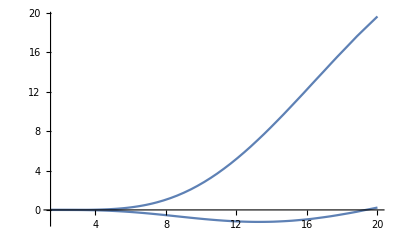

```mathematica
teukint = {r,θ}|->TeukolskyTintegrandExpl[r,θ]*Sin[θ]*PrivateTeukolsky`SWSHS[2][θ];
teukint[3.86,1]
teukint[20,2]
Plot[teukint[r,1]//ReIm, {r,1.45,20}]
```

Comparison of Tlmω

```mathematica
Tlmω[2][3.86]
Tlmω[2]
Plot[Tlmω[2][r]//ReIm, {r,1.44,100}]
```

0.0269771-0.0434657 ⅈ

Comparison of Renormalized angular momentum

```mathematica
TeuInterEnv`νsolIn[2,2][2*TeuInterEnv`wr]//Evaluate
RenormalizedAngularMomentum[-2,2,2,0.9`20.,SetPrecision[4*TeuInterEnv`wr,64],Method->"Monodromy"]
```

RenormalizedAngularMomentum[-2.,2.,2.,0.9,1.1345294414398515,Method→Monodromy]

Comparison of Homogeneous solution of MST

```mathematica
With[{TeuInterEnv`spinin=0.9,TeuInterEnv`wr=0.2836323604304887114412526546297144404`25.150514992000527,TeuInterEnv`rstop = 400},
Off[Power::infy];
MSTgRoots[TeuInterEnv`spinin,-2,2,2,2];
νsol[w_]:=nufullBHPT[w];
MSTSolution[TeuInterEnv`spinin,νsol[2*TeuInterEnv`wr],2*TeuInterEnv`wr,AlmSWSH[2*TeuInterEnv`wr], -2,2,2,TeuInterEnv`rstop];
rsol22 = MSTformalism`Rnumerical;
On[Power::infy];
]
```

λ_(swsh,  MSTpackage): 0.657813089546964

Comparison of Z_lmω integrand

```mathematica
tlmw = TeuInterEnv`Tlmω[2];
Rin = {TeuInterEnv`r}|->TeuInterEnv`RinSet[2,2]//Evaluate;
integrand = {r}|->tlmw[r]*Rin[r]/((r^2-2*r+(0.9)^2)^2);
Plot[integrand[r]//Abs, {r,1.45,100}];
integrand[3.86]
```

0.00114702+0.0666179 ⅈ

Comparison of incoming amplitude

```mathematica
TeuInterEnv`BincSet[2,2]
```

15.557757161322688703-1.268787801534708842 ⅈ

Comparison of Z_lmω

```mathematica
integration = NIntegrate[integrand[rr],{rr,2.5,TeuInterEnv`rstop},MaxRecursion->50,WorkingPrecision->10]
zinf = integration/(2 * I * 2*TeuInterEnv`wr * TeuInterEnv`BincSet[2,2])
```

-0.005698989892+0.00146165492 ⅈ

0.0000561051227+0.0003274510897 ⅈ

```mathematica
3
```